## 显示列表

ListPlot 是显示或可视化数字列表的一种方法。还有很多其他的方法。不同的方法倾向于强调列表的不同特征。

ListLinePlot 用于绘制列表，并把值连接起来：

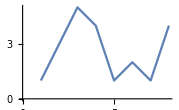

```mathematica
ListLinePlot[{1,3,5,4,1,2,1,4}]
```

当值跳跃时，如果你不把它们连接起来，通常很难理解：

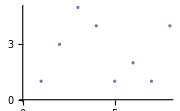

```mathematica
ListPlot[{1,3,5,4,1,2,1,4}]
```

创建条形图也是很有用的：

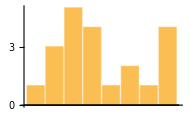

```mathematica
BarChart[{1,3,5,4,1,2,1,4}]
```

只要列表不是太长，饼状图就会很有用：

```mathematica
PieChart[{1,3,5,4}]
```

-Graphics-

如果你只想知道出现了哪些数字，可以把它们画在数轴上：

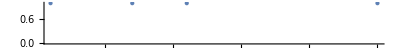

```mathematica
NumberLinePlot[{1,7,11,25}]
```

有时你可能根本不需要绘图；你只想把列表的元素放在一列中：

```mathematica
Column[{100,350,502,400}]
```

100
350
502
400

列表可以包含任何东西，包括图形。因此，你可以把它们放在列表中以组合起来。

创建包含两个饼图的列表：

```mathematica
{PieChart[Range[3]],PieChart[Range[5]]}
```

{-Graphics-,-Graphics-}

将三个柱状图显示在一起：

```mathematica
{BarChart[{1,1,4,2}],BarChart[{5,1,1,0}],BarChart[{1,3,2,4}]}
```

{-Graphics-,-Graphics-,-Graphics-}

词汇

ListLinePlot[{1,2,5}] |   | 用直线来连接值
BarChart[{1,2,5}] |   | 条形图(由值来给定条的长度)
PieChart[{1,2,5}] |   | 饼状图(由值来指定扇形的大小)
NumberLinePlot[{1,2,5}] |   | 将数字排列在数轴上
Column[{1,2,5}] |   | 将元素显示在一列中

"共有 7 道习题"
"以及 6 道附加题" | "开始练习 »"

绘制 {1,1,2,3,5} 的条形图。»

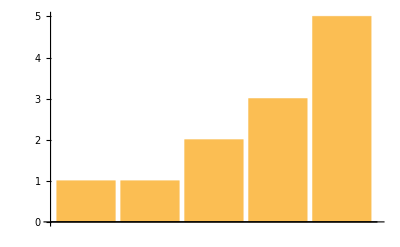
| Expected output: |  
  | -Graphics- |

创建从 1 到 10 的数字的饼图。»

| Expected output: |  
  | -Graphics- |

创建从 20 递减到 1 的数字的条形图。»

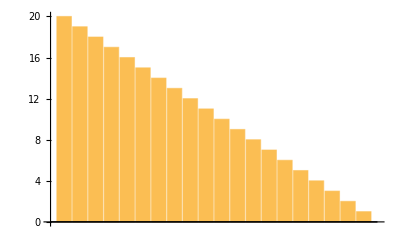
| Expected output: |  
  | -Graphics- |

在一列中显示从 1 到 5 的数字。»

| Expected output: |  
  | 1
2
3
4
5 |

创建 {1,4,9,16,25} 的数轴图。»

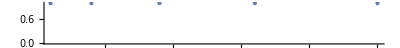
| Expected output: |  
  | -Graphics- |

创建包含 10 个相同段的饼图，每段大小为 1。(提示：使用 Table，详见第 6 节)»

| Expected output: |  
  | -Graphics- |

创建一列饼图，每个图分别包含 1、2、3 个相同段。»

| Expected output: |  
  | -Graphics- |

创建一个饼图列表，每个图分别包含 1、2、3 个相同段。»

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

将 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1 绘制成条形图。»

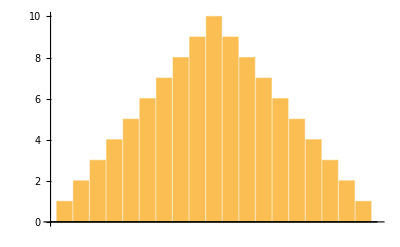
| Expected output: |  
  | -Graphics- |

创建一个列表，包含由 1 到 10 的数字创建的饼图、条形图和线条图。»

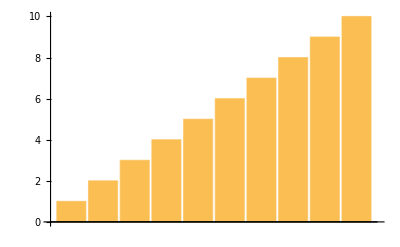
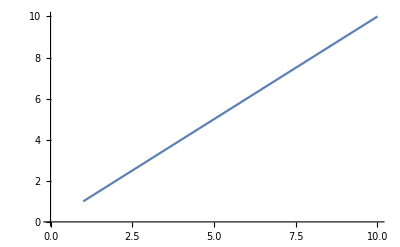
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

创建一个列表，包含 {1,1,2,3,5,8,13,21,34,55} 创建的饼图和条形图。»

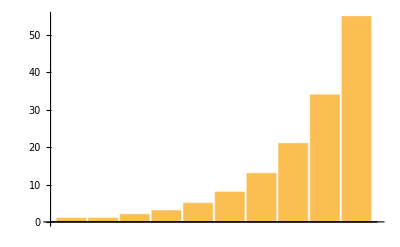
| Expected output: |  
  | {-Graphics-,-Graphics-} |

创建一个列，包含两条由 {1,2,3,4,5} 绘制的数轴图。»

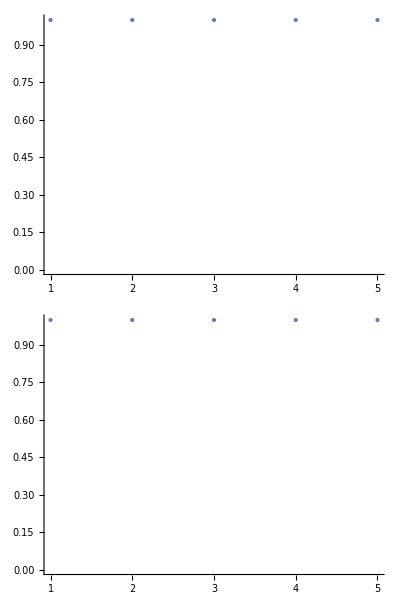
| Expected output: |  
  | -Graphics- |

创建从 1/2, 1/3, ... 到 1/9 的数轴图。»

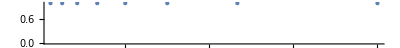
| Expected output: |  
  | -Graphics- |

问&答

饼状图在 Wolfram 语言中是如何工作的？

在任何饼图中，扇形的相对大小由列表中的数字的相对大小决定。在 Wolfram 语言中，第一个数字的扇形从 9 点钟的位置开始，后续的扇形按顺时针方向来读取。扇形的颜色是按照一定的顺序选择的。

绘图在竖直方向上的比例是如何确定的？

它被设置为自动包括所有的点，除了非常远的离群值。稍后(第20节)，我们将讨论 PlotRange 选项，它可以让你指定绘图的精确范围。

技术笔记

特别是如果你熟悉其他计算机语言，你可能会感到惊讶，例如，列表的绘图可以作为一个计算的输出。这是由 Wolfram 语言是符号语言的这一关键事实所决定的。顺便说一下，绘图也可以出现在输入中。

探索更多

Wolfram 语言中的数据可视化 »

Wolfram 语言中的图表和信息可视化 »